# 2.1 Hmwk - Freq Distr, Histograms, &amp; Related (Homework)

## Question 7

How long does it take to finish the 1161-mile Iditarod Dog Sled Race from Anchorage to Nome, Alaska? Finish times (to the nearest hour) for 57 dogsled teams are shown below.

```mathematica
IditarodData=Flatten[{{261,271,236,244,279,296,284,299,288},{288,247,256,338,360,341,333,261,266},{287,296,313,311,307,307,299,303,277},{283,304,305,288,290,288,289,297,299},{332,330,309,328,307,328,285,291,295},{298,306,315,310,318,318,320,333,321},{323,324,327}}];
```

classwidth=(largest value-smallest value)/(desired number of classes).

If this is a whole number, increase the number to the next whole number.

```mathematica
ClassWidthUnrounded[data_,classes_]:=N@((Max[data]-Min[data])/classes)
```

```mathematica
ClassWidthUnrounded[IditarodData,5]
```

24.8

```mathematica
ClassWithRoundedToNearestWholeNumber[data_,classes_]:=Block[{classWidthUnrounded},classWidthUnrounded=N@((Max[data]-Min[data])/classes);If[IntegerQ[classWidthUnrounded],classWidthUnrounded+1,⌈classWidthUnrounded⌉]]
```

```mathematica
ClassWithRoundedToNearestWholeNumber[IditarodData,5]
```

25

```mathematica
ClassWithRoundedToNearestWholeNumber[Range[5],4]
```

1

```mathematica
⌈3⌉
⌈⌈3⌉⌉
```

3

3

```mathematica
⌈2.7⌉
⌈⌈2.7⌉⌉
```

3

3

```mathematica
BinLists[IditarodData,ClassWithRoundedToNearestWholeNumber[IditarodData,5]]
```

{{236,244,247},{261,271,256,261,266},{279,296,284,299,288,288,287,296,299,277,283,288,290,288,289,297,299,285,291,295,298},{313,311,307,307,303,304,305,309,307,306,315,310,318,318,320,321,323,324},{338,341,333,332,330,328,328,333,327},{360}}

```mathematica
Length/@BinLists[IditarodData,ClassWithRoundedToNearestWholeNumber[IditarodData,5]]
```

{3,5,21,18,9,1}

```mathematica
Total[{3,5,21,18,9,1}]
```

57

```mathematica
Length/@BinLists[IditarodData,{Min[IditarodData],Max[IditarodData],ClassWithRoundedToNearestWholeNumber[IditarodData,5]}]
```

{4,9,25,16}

```mathematica
Total[Length/@BinLists[IditarodData,{Min[IditarodData],Max[IditarodData],ClassWithRoundedToNearestWholeNumber[IditarodData,5]}]]
```

54

```mathematica
Total[{4,9,25,16,3}]
```

57

```mathematica
6*9+3
```

57

```mathematica
Length[IditarodData]
```

57

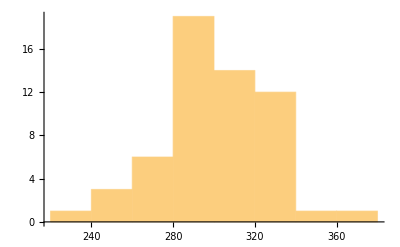

```mathematica
Histogram[IditarodData]
```

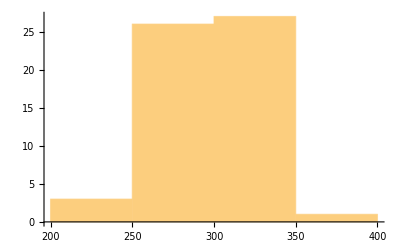
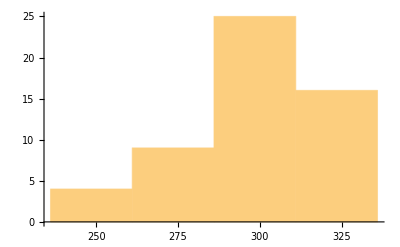
<|Sturges→-Graphics-,Scott→-Graphics-,FreedmanDiaconis→-Graphics-,Knuth→-Graphics-,Wand→-Graphics-,3→-Graphics-,4→-Graphics-,5→-Graphics-,{236,360,25}→-Graphics-|>

```mathematica
AssociationMap[Histogram[IditarodData,#]&,{"Sturges","Scott","FreedmanDiaconis","Knuth","Wand",3,4,5,{Min[IditarodData],Max[IditarodData],25}}]
```

```mathematica
Histogram[IditarodData,{Min[IditarodData],Max[IditarodData],25}]
```

-Graphics-

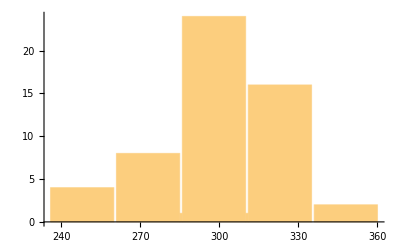

```mathematica
Histogram[IditarodData,{{236,260,261,285,286,310,311,335,336,360}}]
```

```mathematica
Histogram[IditarodData,{{235.5,260.5,260.5,285.5,285.5,310.5,310.5,335.5,335.5,360.5}}]
```

Histogram::hbins: The bin specification {{235.5,260.5,260.5,285.5,285.5,310.5,310.5,335.5,335.5,360.5}} cannot be used to determine either how many or which bins to use.

Histogram[{261,271,236,244,279,296,284,299,288,288,247,256,338,360,341,333,261,266,287,296,313,311,307,307,299,303,277,283,304,305,288,290,288,289,297,299,332,330,309,328,307,328,285,291,295,298,306,315,310,318,318,320,333,321,323,324,327},{{235.5,260.5,260.5,285.5,285.5,310.5,310.5,335.5,335.5,360.5}}]

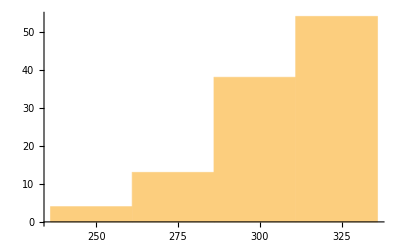
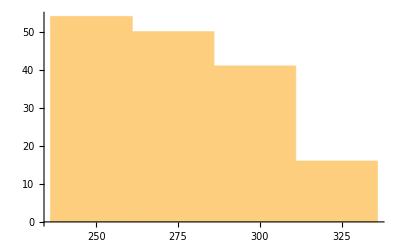
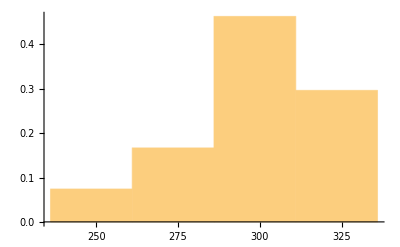
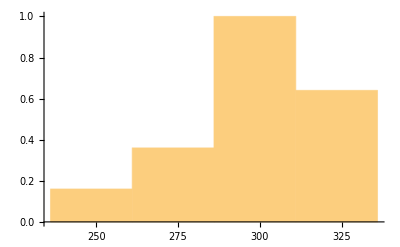
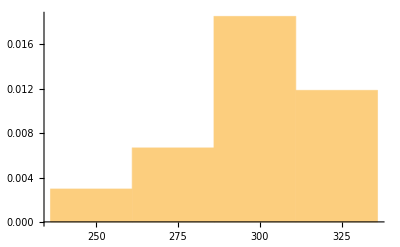
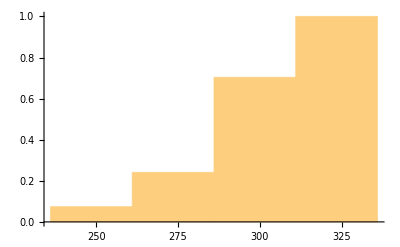
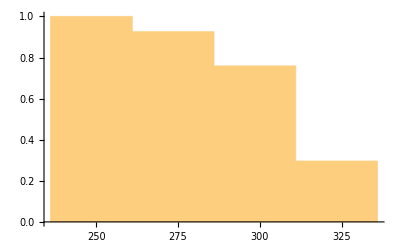
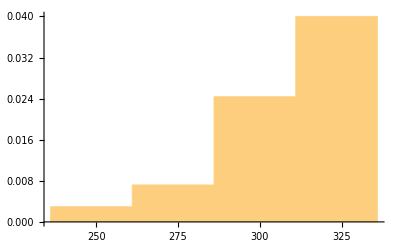
<|Count→-Graphics-,CumulativeCount→-Graphics-,SurvivalCount→-Graphics-,Probability→-Graphics-,Intensity→-Graphics-,PDF→-Graphics-,CDF→-Graphics-,SF→-Graphics-,HF→-Graphics-,CHF→-Graphics-|>

```mathematica
AssociationMap[Histogram[IditarodData,{Min[IditarodData],Max[IditarodData],25},#]&,{"Count","CumulativeCount","SurvivalCount","Probability","Intensity","PDF","CDF","SF","HF","CHF"}]
```

```mathematica
Min[IditarodData]
```

236

```mathematica
Max[IditarodData]
```

360

```mathematica
BinLists[IditarodData]
```

{{},{236},{},{},{},{},{},{},{},{244},{},{},{247},{},{},{},{},{},{},{},{},{256},{},{},{},{},{261,261},{},{},{},{},{266},{},{},{},{},{271},{},{},{},{},{},{277},{},{279},{},{},{},{283},{284},{285},{},{287},{288,288,288,288},{289},{290},{291},{},{},{},{295},{296,296},{297},{298},{299,299,299},{},{},{},{303},{304},{305},{306},{307,307,307},{},{309},{310},{311},{},{313},{},{315},{},{},{318,318},{},{320},{321},{},{323},{324},{},{},{327},{328,328},{},{330},{},{332},{333,333},{},{},{},{},{338},{},{},{341},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{360}}

```mathematica
BinLists[IditarodData,25]
```

{{236,244,247},{261,271,256,261,266},{279,296,284,299,288,288,287,296,299,277,283,288,290,288,289,297,299,285,291,295,298},{313,311,307,307,303,304,305,309,307,306,315,310,318,318,320,321,323,324},{338,341,333,332,330,328,328,333,327},{360}}

```mathematica
BinLists[IditarodData,{236,360,25}]
```

{{236,244,247,256},{261,271,279,284,261,266,277,283,285},{296,299,288,288,287,296,307,307,299,303,304,305,288,290,288,289,297,299,309,307,291,295,298,306,310},{333,313,311,332,330,328,328,315,318,318,320,333,321,323,324,327}}

```mathematica
BinLists[IditarodData,{{235.5,260.5,285.5,310.5,335.5,360.5}}]
```

{{236,244,247,256},{261,271,279,284,261,266,277,283,285},{296,299,288,288,287,296,307,307,299,303,304,305,288,290,288,289,297,299,309,307,291,295,298,306,310},{333,313,311,332,330,328,328,315,318,318,320,333,321,323,324,327},{338,360,341}}

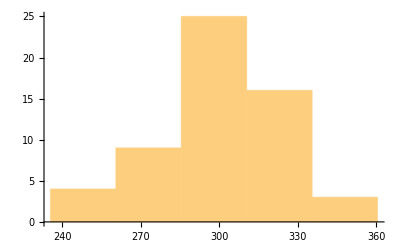

```mathematica
Histogram[IditarodData,{{235.5,260.5,285.5,310.5,335.5,360.5}}]
```

```mathematica
BinLists[Range[236,360],{236,360,25}]
```

{{236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260},{261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285},{286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310},{311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335}}

```mathematica
ClassLimits[data_,classes_]:=Block[{classWidthUnrounded,classWidth,min,max,MostClassLimits},min=Min[data];max=Max[data];classWidthUnrounded=N@((max-min)/classes);classWidth=If[IntegerQ[classWidthUnrounded],classWidthUnrounded+1,⌈classWidthUnrounded⌉];MostClassLimits={First[#],Last[#]}&/@BinLists[Range[min,max],{min,max,classWidth}];Join[MostClassLimits,{{MostClassLimits[[-2,2]]+classWidth+1,Last[MostClassLimits][[2]]+classWidth}}]]
```

```mathematica
ClassBoundaries[data_,classes_?IntegerQ]:=Block[{classWidthUnrounded,classWidth,min,max,MostClassLimits,classLimits},min=Min[data];max=Max[data];classWidthUnrounded=N@((max-min)/classes);classWidth=If[IntegerQ[classWidthUnrounded],classWidthUnrounded+1,⌈classWidthUnrounded⌉];MostClassLimits={First[#],Last[#]}&/@BinLists[Range[min,max],{min,max,classWidth}];classLimits=Join[MostClassLimits,{{MostClassLimits[[-2,2]]+classWidth+1,Last[MostClassLimits][[2]]+classWidth}}];Transpose[{classLimits[[All,1]]-0.5,classLimits[[All,2]]+0.5}]]
```

```mathematica
ClassLimits[IditarodData,5]
```

{{236,260},{261,285},{286,310},{311,335},{336,360}}

```mathematica
ClassLimits[IditarodData,5][[All,1]]-0.5
```

{235.5,260.5,285.5,310.5,335.5}

```mathematica
ClassLimits[IditarodData,5][[All,2]]+0.5
```

{260.5,285.5,310.5,335.5,360.5}

```mathematica
Transpose[{ClassLimits[IditarodData,5][[All,1]]-0.5,ClassLimits[IditarodData,5][[All,2]]+0.5}]
```

{{235.5,260.5},{260.5,285.5},{285.5,310.5},{310.5,335.5},{335.5,360.5}}

```mathematica
(360-236)/5.
```

24.8

```mathematica
ClassBoundaries[IditarodData,5]
```

{{235.5,260.5},{260.5,285.5},{285.5,310.5},{310.5,335.5},{335.5,360.5}}

```mathematica
FrequencyTableMidpoint[data_List,classes_?IntegerQ]:=Block[{classWidthUnrounded,classWidth,min,max,MostClassLimits,classLimits,classBoundaries},min=Min[data];max=Max[data];classWidthUnrounded=N@((max-min)/classes);classWidth=If[IntegerQ[classWidthUnrounded],classWidthUnrounded+1,⌈classWidthUnrounded⌉];MostClassLimits={First[#],Last[#]}&/@BinLists[Range[min,max],{min,max,classWidth}];classLimits=Join[MostClassLimits,{{MostClassLimits[[-2,2]]+classWidth+1,Last[MostClassLimits][[2]]+classWidth}}];classBoundaries=Transpose[{classLimits[[All,1]]-0.5,classLimits[[All,2]]+0.5}];(First[#]+Last[#])/2&/@classLimits]
```

```mathematica
FrequencyTableFrequency[data_List,classes_?IntegerQ]:=Block[{classWidthUnrounded,classWidth,min,max,MostClassLimits,classLimits,classBoundaries,midpoints},min=Min[data];max=Max[data];classWidthUnrounded=N@((max-min)/classes);classWidth=If[IntegerQ[classWidthUnrounded],classWidthUnrounded+1,⌈classWidthUnrounded⌉];MostClassLimits={First[#],Last[#]}&/@BinLists[Range[min,max],{min,max,classWidth}];classLimits=Join[MostClassLimits,{{MostClassLimits[[-2,2]]+classWidth+1,Last[MostClassLimits][[2]]+classWidth}}];classBoundaries=Transpose[{classLimits[[All,1]]-0.5,classLimits[[All,2]]+0.5}];midpoints=(First[#]+Last[#])/2&/@classLimits;Join[BinCounts[data,{classLimits[[All,1]]}],{Length[data]-Total[BinCounts[data,{classLimits[[All,1]]}]]}]]
```

```mathematica
FrequencyTableRelativeFrequency[data_List,classes_?IntegerQ]:=Block[{classWidthUnrounded,classWidth,min,max,MostClassLimits,classLimits,classBoundaries,midpoints,frequency,relativeFrequency,cumulativeFrequency,cumulativeRelativeFrequency},min=Min[data];max=Max[data];classWidthUnrounded=N@((max-min)/classes);classWidth=If[IntegerQ[classWidthUnrounded],classWidthUnrounded+1,⌈classWidthUnrounded⌉];MostClassLimits={First[#],Last[#]}&/@BinLists[Range[min,max],{min,max,classWidth}];classLimits=Join[MostClassLimits,{{MostClassLimits[[-2,2]]+classWidth+1,Last[MostClassLimits][[2]]+classWidth}}];classBoundaries=Transpose[{classLimits[[All,1]]-0.5,classLimits[[All,2]]+0.5}];midpoints=(First[#]+Last[#])/2&/@classLimits;frequency=Join[BinCounts[data,{classLimits[[All,1]]}],{Length[data]-Total[BinCounts[data,{classLimits[[All,1]]}]]}];N[#/Length[data]]&/@frequency]
```

```mathematica
FrequencyTableCumulativeFrequency[data_List,classes_?IntegerQ]:=Block[{classWidthUnrounded,classWidth,min,max,MostClassLimits,classLimits,classBoundaries,midpoints,frequency,relativeFrequency,cumulativeFrequency,cumulativeRelativeFrequency},min=Min[data];max=Max[data];classWidthUnrounded=N@((max-min)/classes);classWidth=If[IntegerQ[classWidthUnrounded],classWidthUnrounded+1,⌈classWidthUnrounded⌉];MostClassLimits={First[#],Last[#]}&/@BinLists[Range[min,max],{min,max,classWidth}];classLimits=Join[MostClassLimits,{{MostClassLimits[[-2,2]]+classWidth+1,Last[MostClassLimits][[2]]+classWidth}}];classBoundaries=Transpose[{classLimits[[All,1]]-0.5,classLimits[[All,2]]+0.5}];midpoints=(First[#]+Last[#])/2&/@classLimits;frequency=Join[BinCounts[data,{classLimits[[All,1]]}],{Length[data]-Total[BinCounts[data,{classLimits[[All,1]]}]]}];relativeFrequency=N[#/Length[data]]&/@frequency;Accumulate[frequency]]
```

```mathematica
FrequencyTableCumulativeRelativeFrequency[data_List,classes_?IntegerQ]:=Block[{classWidthUnrounded,classWidth,min,max,MostClassLimits,classLimits,classBoundaries,midpoints,frequency,relativeFrequency,cumulativeFrequency,cumulativeRelativeFrequency},min=Min[data];max=Max[data];classWidthUnrounded=N@((max-min)/classes);classWidth=If[IntegerQ[classWidthUnrounded],classWidthUnrounded+1,⌈classWidthUnrounded⌉];MostClassLimits={First[#],Last[#]}&/@BinLists[Range[min,max],{min,max,classWidth}];classLimits=Join[MostClassLimits,{{MostClassLimits[[-2,2]]+classWidth+1,Last[MostClassLimits][[2]]+classWidth}}];classBoundaries=Transpose[{classLimits[[All,1]]-0.5,classLimits[[All,2]]+0.5}];midpoints=(First[#]+Last[#])/2&/@classLimits;frequency=Join[BinCounts[data,{classLimits[[All,1]]}],{Length[data]-Total[BinCounts[data,{classLimits[[All,1]]}]]}];relativeFrequency=N[#/Length[data]]&/@frequency;cumulativeFrequency=Accumulate[frequency];cumulativeRelativeFrequency=Accumulate[relativeFrequency]]
```

```mathematica
FrequencyTableData[data_List,classes_?IntegerQ]:=Block[{classWidthUnrounded,classWidth,min,max,MostClassLimits,classLimits,classBoundaries,midpoints,frequency,relativeFrequency,cumulativeFrequency,cumulativeRelativeFrequency,histogram,relativeFrequencyHistogram,cumulativeFrequencyHistogram,relativeCumulativeFrequencyHistogram},min=Min[data];max=Max[data];classWidthUnrounded=N@((max-min)/classes);classWidth=If[IntegerQ[classWidthUnrounded],classWidthUnrounded+1,⌈classWidthUnrounded⌉];MostClassLimits={First[#],Last[#]}&/@BinLists[Range[min,max],{min,max,classWidth}];classLimits=Join[MostClassLimits,{{MostClassLimits[[-2,2]]+classWidth+1,Last[MostClassLimits][[2]]+classWidth}}];classBoundaries=Transpose[{classLimits[[All,1]]-0.5,classLimits[[All,2]]+0.5}];midpoints=(First[#]+Last[#])/2&/@classLimits;frequency=Join[BinCounts[data,{classLimits[[All,1]]}],{Length[data]-Total[BinCounts[data,{classLimits[[All,1]]}]]}];relativeFrequency=N[#/Length[data]]&/@frequency;cumulativeFrequency=Accumulate[frequency];cumulativeRelativeFrequency=Accumulate[relativeFrequency];histogram=Histogram[data,{Union[classBoundaries[[All,1]],classBoundaries[[All,-1]]]}];relativeFrequencyHistogram=Histogram[data,{Union[classBoundaries[[All,1]],classBoundaries[[All,-1]]]},"Probability"];cumulativeFrequencyHistogram=Histogram[data,{Union[classBoundaries[[All,1]],classBoundaries[[All,-1]]]},"CumulativeCount"];relativeCumulativeFrequencyHistogram=Histogram[data,{Union[classBoundaries[[All,1]],classBoundaries[[All,-1]]]},"CDF"];<|"ClassWidth"->classWidth,"ClassLimits"->classLimits,"ClassBoundaries"->classBoundaries,"Midpoints"->midpoints,"Frequency"->frequency,"RelativeFrequency"->relativeFrequency,"CumulativeFrequency"->cumulativeFrequency,"CumulativeRelativeFrequency"->cumulativeRelativeFrequency,"Histogram"->histogram,"RelativeFrequencyHistogram"->relativeFrequencyHistogram,"CumulativeFrequencyHistogram"->cumulativeFrequencyHistogram,"RelativeCumulativeFrequencyHistogram"->relativeCumulativeFrequencyHistogram|>]
```

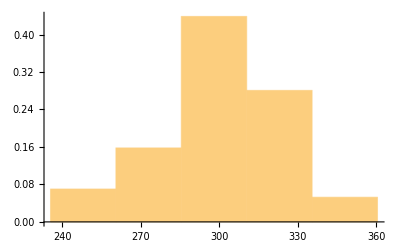
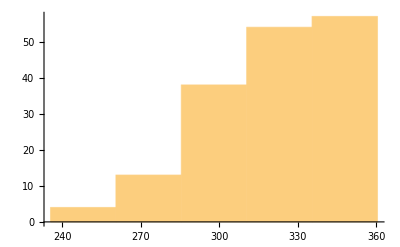
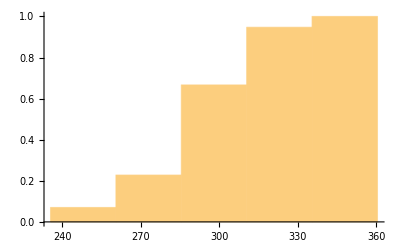
<|ClassWidth→25,ClassLimits→{{236,260},{261,285},{286,310},{311,335},{336,360}},ClassBoundaries→{{235.5,260.5},{260.5,285.5},{285.5,310.5},{310.5,335.5},{335.5,360.5}},Midpoints→{248,273,298,323,348},Frequency→{4,9,25,16,3},RelativeFrequency→{0.0701754,0.157895,0.438596,0.280702,0.0526316},CumulativeFrequency→{4,13,38,54,57},CumulativeRelativeFrequency→{0.0701754,0.22807,0.666667,0.947368,1.},Histogram→-Graphics-,RelativeFrequencyHistogram→-Graphics-,CumulativeFrequencyHistogram→-Graphics-,RelativeCumulativeFrequencyHistogram→-Graphics-|>

```mathematica
FrequencyTableData[IditarodData,5]
```

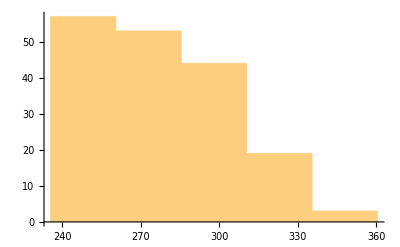
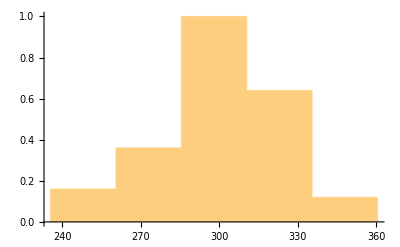
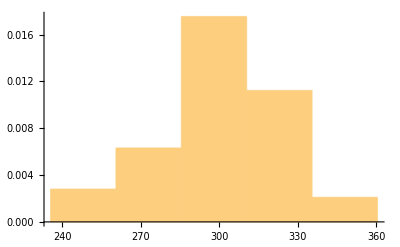
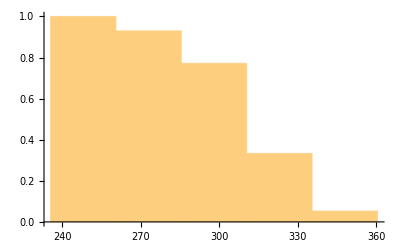
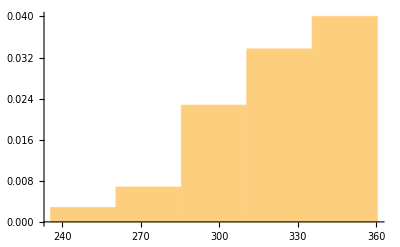
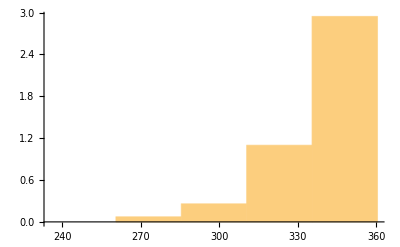
<|Count→-Graphics-,CumulativeCount→-Graphics-,SurvivalCount→-Graphics-,Probability→-Graphics-,Intensity→-Graphics-,PDF→-Graphics-,CDF→-Graphics-,SF→-Graphics-,HF→-Graphics-,CHF→-Graphics-|>

```mathematica
AssociationMap[Histogram[IditarodData,{{235.5,260.5,285.5,310.5,335.5,360.5}},#]&,{"Count","CumulativeCount","SurvivalCount","Probability","Intensity","PDF","CDF","SF","HF","CHF"}]
```

```mathematica
Union[ClassBoundaries[IditarodData,5][[All,1]],ClassBoundaries[IditarodData,5][[All,-1]]]
```

{235.5,260.5,285.5,310.5,335.5,360.5}

```mathematica
FrequencyTableCumulativeRelativeFrequency[IditarodData,5]
```

{0.0701754,0.22807,0.666667,0.947368,1.}

```mathematica
FrequencyTableCumulativeFrequency[IditarodData,5]
```

{4,13,38,54,57}

```mathematica
FrequencyTableRelativeFrequency[IditarodData,5]
```

{0.0701754,0.157895,0.438596,0.280702,0.0526316}

```mathematica
(First[#]+Last[#])/2&/@ClassLimits[IditarodData,5]
```

{248,273,298,323,348}

```mathematica
(336+360)/2
```

348

```mathematica
FrequencyTableMidpoint[IditarodData,5]
```

{248,273,298,323,348}

```mathematica
FrequencyTableFrequency[IditarodData,5]
```

{4,9,25,16,3}

```mathematica
ClassLimits[IditarodData,5][[All,1]]
ClassBoundaries[IditarodData,5][[All,1]]
Join[ClassLimits[IditarodData,5][[All,1]],ClassLimits[IditarodData,5][[-1,1]]]
```

{236,261,286,311,336}

{235.5,260.5,285.5,310.5,335.5}

{236,261,286,311,336}

```mathematica
BinCounts[IditarodData,{Join[ClassLimits[IditarodData,5][[All,1]],ClassLimits[IditarodData,5][[-1,1]]]}]
```

{4,9,25,16}

```mathematica
BinCounts[IditarodData,{ClassLimits[IditarodData,5][[All,1]]}]
```

{4,9,25,16}

```mathematica
Join[BinCounts[IditarodData,{ClassLimits[IditarodData,5][[All,1]]}],{Length[IditarodData]-Total[BinCounts[IditarodData,{ClassLimits[IditarodData,5][[All,1]]}]]}]
```

{4,9,25,16,3}

```mathematica
Total[{4,9,25,16}]
```

54

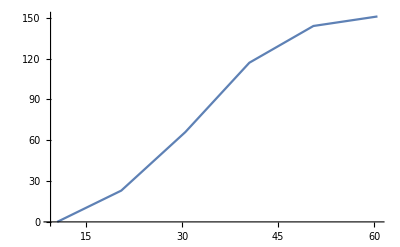

```mathematica
ListLinePlot[{{10.5,0},{20.5,23},{30.5,66},{40.5,117},{50.5,144},{60.5,151}}]
```

## Histogram

The following data represent tonnes of wheat harvest each year (1894-1925) from Plot 19 at the Rothamsted Agricultural Experiment Stations, England.

```mathematica
WheatHarvestRothamsted1894To1925Data=Flatten[{{2.71,1.62,2.60,1.64,2.20,2.02,1.67,1.99,2.34,1.26,1.31},{1.80,2.82,2.15,2.07,1.62,1.47,2.19,0.59,1.48,0.77,2.04},{1.32,0.89,1.35,0.95,0.94,1.39,1.19,1.18,0.46,0.70}}];
```

```mathematica
WheatHarvestRothamsted1894To1925DataIntegers=100WheatHarvestRothamsted1894To1925Data;
```

```mathematica
ClassLimits[WheatHarvestRothamsted1894To1925DataIntegers,6]
```

{{46.,85.},{86.,125.},{126.,165.},{166.,205.},{206.,245.},{246.,285.}}

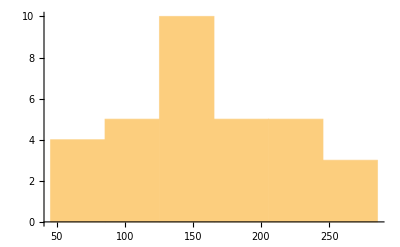
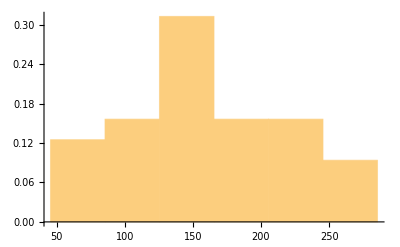
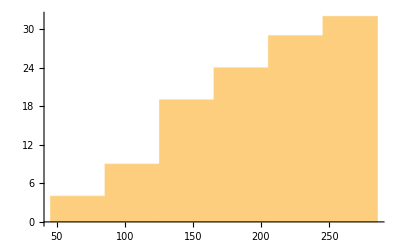
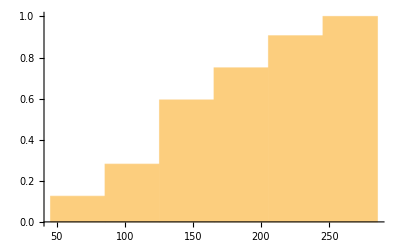
<|ClassWidth→40,ClassLimits→{{46.,85.},{86.,125.},{126.,165.},{166.,205.},{206.,245.},{246.,285.}},ClassBoundaries→{{45.5,85.5},{85.5,125.5},{125.5,165.5},{165.5,205.5},{205.5,245.5},{245.5,285.5}},Midpoints→{65.5,105.5,145.5,185.5,225.5,265.5},Frequency→{4,5,10,5,5,3},RelativeFrequency→{0.125,0.15625,0.3125,0.15625,0.15625,0.09375},CumulativeFrequency→{4,9,19,24,29,32},CumulativeRelativeFrequency→{0.125,0.28125,0.59375,0.75,0.90625,1.},Histogram→-Graphics-,RelativeFrequencyHistogram→-Graphics-,CumulativeFrequencyHistogram→-Graphics-,RelativeCumulativeFrequencyHistogram→-Graphics-|>

```mathematica
FrequencyTableData[WheatHarvestRothamsted1894To1925DataIntegers,6]
```